# Wind Turbine Designer Tool

## Math Model

### Constants

#### Air Density (δa)

```mathematica
δa=1.225;
```

```mathematica
CPmax = 0.5925925925925926;
```

### Equations

#### Wind Power

```mathematica
Pw[Vw_, R_, CP_]:= 1/2 CP δa Vw^3 R^2 π;
```

#### Rotor radius

```mathematica
RotorRadius[Po_,  Vw_, Cp_]:=√((2*Po)/(δa * Vw^3*Cp * π));
```

#### Tip Speed Ratio (λ)

```mathematica
TSR[Vw_, rpm_, R_]:= R*rpm*π / (Vw * 30);
```

#### Revolutions Per Minutes

```mathematica
RPM[Vw_, λ_,  R_]:= (λ * 30 * Vw)/(R*π);
```

```mathematica
RPM2[Vw_, rpmmax_,λ_,R_]:= Piecewise[{{RPM[Vw,λ, R], RPM[Vw,λ, R] ≤rpmmax  }, {rpmmax,  RPM[Vw,λ, R]>rpmmax}}]
```

#### Average Chord Length

```mathematica
AverageChordLength[R_,Sp_,Cl_,Z_]:=(R * Sp)/(Cl * Z);
```

#### Chord Length List

```mathematica
ChordLength[R_, Vw_, Z_, Cl_, λ_, Vr_]:=(2 π R 8 Vw)/(Z 9 Cl λ Vr);
```

#### Solidity

```mathematica
Solidity[R_,l_,Z_]:=(Z*l)/(π*R);
```

#### Blade Velocity

```mathematica
Vu[ R_, rpm_]:=R*rpm*π/30;
```

#### Relative Wind Velocity

```mathematica
Vr[Vw_, Vu_]:=√((2/3 Vw)^2+ Vu^2);
```

#### Wind Angle (θ)

```mathematica
theta[λr_]:=ArcTan[2/(3 λr)]/ Degree;
```

#### Forces on the Blade

```mathematica
Fblade[CFT_, Vr_, L_, dr_]:=1/2 CFT δa Vr^2 L dr;
```

## Airfoil Data

### Airfoil Specifications: A18

#### Aerodynamic Data

```mathematica
A18AlphaData=List[-9.25,-9.0,-8.75,-8.5,-8.25,-8.0,-7.75,-7.5,-7.25,-7.0,-6.75,-6.5,-6.25,-6.0,-5.75,-5.5,-5.25,-5.0,-4.75,-4.5,-4.25,-4.0,-3.75,-3.5,-3.25,-3.0,-2.75,-2.5,-2.25,-2.0,-1.75,-1.5,-1.25,-1.0,-0.75,-0.5,-0.25,0.0,0.25,0.5,0.75,1.0,1.25,1.5,1.75,2.0,2.25,2.5,2.75,3.0,3.25,3.5,3.75,4.0,4.25,4.5,4.75,5.0,5.25,5.5,5.75,6.0,6.25,6.5,6.75,7.0,7.25,7.5,7.75,8.0,8.25,8.5,8.75,9.0,9.25,9.5,9.75,10.0,10.25,10.5,10.75,11.0,11.25,11.5,11.75,12.0,12.25];
A18CLData=List[-0.4152,-0.4198,-0.4263,-0.4291,-0.4307,-0.4302,-0.4264,-0.414,-0.3984,-0.3732,-0.3239,-0.3032,-0.2712,-0.249,-0.2208,-0.1945,-0.1688,-0.1367,-0.0972,-0.0597,-0.0211,0.0151,0.0529,0.0883,0.1259,0.1605,0.1967,0.2324,0.2663,0.3047,0.3362,0.3732,0.4014,0.4255,0.4599,0.4909,0.5229,0.5555,0.5872,0.6172,0.6473,0.6773,0.7071,0.7352,0.7638,0.7912,0.8185,0.8454,0.8718,0.8977,0.9233,0.9484,0.9726,0.9954,1.0168,1.0359,1.0492,1.0649,1.0841,1.1005,1.1157,1.1326,1.1492,1.1656,1.1803,1.1938,1.2102,1.2263,1.2432,1.2603,1.2757,1.2876,1.2958,1.3,1.2991,1.2922,1.282,1.2694,1.2548,1.239,1.2217,1.2039,1.1856,1.1661,1.1459,1.123,1.0913];
A18CDData=List[0.09313,0.08991,0.08677,0.08301,0.07885,0.07409,0.06779,0.05704,0.05493,0.04704,0.03067,0.03073,0.02698,0.02664,0.02517,0.02368,0.02283,0.02195,0.0208,0.01986,0.01917,0.01858,0.01808,0.01764,0.01717,0.01677,0.01639,0.01607,0.01581,0.01544,0.01519,0.0147,0.01416,0.0133,0.01327,0.01328,0.01326,0.01324,0.01323,0.01326,0.0133,0.01331,0.01332,0.01337,0.01344,0.01357,0.01373,0.01391,0.01412,0.01436,0.01462,0.01492,0.0153,0.01577,0.01629,0.01712,0.01861,0.0201,0.02118,0.0226,0.02423,0.02563,0.02699,0.02837,0.02992,0.03172,0.03332,0.03526,0.03745,0.03989,0.04248,0.04497,0.04748,0.05036,0.05378,0.05717,0.06065,0.06432,0.06827,0.07252,0.07726,0.08248,0.08831,0.09501,0.10279,0.11244,0.12734];
```

#### Lift Coefficient (CL) in function of attact angle (α)

```mathematica
A18FCL = Interpolation[Thread[{A18AlphaData, A18CLData}]];
```

#### Drag Coefficient (CD) in function of attact angle (α)

```mathematica
A18FCD= Interpolation[Thread[{A18AlphaData, A18CDData}]];
```

#### Plotting Functions

```mathematica
Show[ Plot[{Labeled[A18FCL[α],"CL"], Labeled[A18FCD[α],"CD"]},{α, -9.5, 12.5}, AxesLabel->{"Angel α","Coefficient"}]]
```

InterpolatingFunction::dmval: Input value {-9.49955} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### Airfoil Geometry

```mathematica
A18Geometry = List[{1.00000000,0.00614000},{0.94999999,0.01817000},{0.89999998,0.02858000},{0.80000001,0.04624000},{0.69999999,0.06056000},{0.60000002,0.07197000},{0.55000001,0.07612000},{0.50000000,0.07975000},{0.44999999,0.08293000},{0.40000001,0.08376000},{0.34999999,0.08466000},{0.30000001,0.08383000},{0.25000000,0.08065000},{0.20000000,0.07601000},{0.15000001,0.07026000},{0.10000000,0.06234000},{0.07500000,0.05660000},{0.05000000,0.04923000},{0.02500000,0.03947000},{0.01250000,0.03239000},{0.00000000,0.01865000},{0.01250000,0.00781000},{0.02500000,0.00357000},{0.05000000,0.00075000},{0.07500000,0.00000000},{0.10000000,0.00006000},{0.15000001,0.00200000},{0.20000000,0.00475000},{0.25000000,0.00806000},{0.30000001,0.01038000},{0.34999999,0.01353000},{0.40000001,0.01657000},{0.44999999,0.01780000},{0.50000000,0.01884000},{0.55000001,0.01980000},{0.60000002,0.01998000},{0.69999999,0.01924000},{0.80000001,0.01452000},{0.89999998,0.00813000},{0.94999999,0.00434000},{1.00000000,0.00000000}];
```

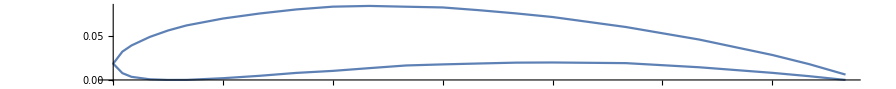

```mathematica
ListLinePlot[A18Geometry, AspectRatio->.1]
```

## Designer

### Design Parameters

#### Air Velocity

```mathematica
Vw = 15;
```

#### Proposed RPM

```mathematica
rpm1 =750;
```

#### Number of Blades

```mathematica
Z1 = 3;
```

#### Number of Ribs (Blade Sections)

```mathematica
Nr = 20;
```

#### Design Power

```mathematica
Pd = 5000;
```

### Common Calculations

#### Calculate the rotor radius

```mathematica
R1 = Round[RotorRadius[Pd, Vw , .45], .01]
```

1.31

#### Calculate the “Tip Speed Ratio” (λ)

```mathematica
λd = TSR[Vw, rpm1, R1]
```

6.85914

```mathematica
TSRD[V_]:= Piecewise[{{λd,RPM[V,λd, R1] ≤ rpm1},{ TSR[V, rpm1, R1],RPM[V,λd, R1] > rpm1}}];
```

#### Differential of the radius (Δr)

```mathematica
Δr =(R1 - 0.10*R1) / (Nr -1)
```

0.0620526

#### Vector of ribs radius

```mathematica
Rb = Table[x,{x,R1 - Δr*(Nr-1),  R1,Δr  }]
```

{0.131,0.193053,0.255105,0.317158,0.379211,0.441263,0.503316,0.565368,0.627421,0.689474,0.751526,0.813579,0.875632,0.937684,0.999737,1.06179,1.12384,1.18589,1.24795,1.31}

#### Calculating the blade velocity list

```mathematica
Vus1 =Vu[Rb, rpm1]
```

{10.2887,15.1623,20.0359,24.9095,29.7831,34.6567,39.5303,44.4039,49.2775,54.1511,59.0247,63.8983,68.7719,73.6455,78.5191,83.3928,88.2664,93.14,98.0136,102.887}

#### Calculating the relative wind velocity list

```mathematica
Vrs1 = Vr[Vw ,Vus1]
```

{14.3477,18.163,22.3928,26.8418,31.4171,36.0706,40.7756,45.516,50.282,55.0667,59.8658,64.6761,69.4952,74.3214,79.1534,83.9902,88.831,93.6752,98.5224,103.372}

#### Calculating the speed ratio list

```mathematica
λr1  = λd *Rb /R1
```

{0.685914,1.01082,1.33573,1.66063,1.98554,2.31045,2.63536,2.96026,3.28517,3.61008,3.93498,4.25989,4.5848,4.9097,5.23461,5.55952,5.88442,6.20933,6.53424,6.85914}

#### Calculating the relative air angle

```mathematica
θs1 = theta[λr1]
```

{44.1847,33.406,26.5239,21.8731,18.56,16.0952,14.1963,12.6916,11.4714,10.4628,9.61577,8.89456,8.27329,7.73265,7.25797,6.83794,6.46368,6.1281,5.82554,5.55136}

#### Common Parameters

```mathematica
getMaxValue1[function_]:=FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[1]];
```

```mathematica
getMaxValue2[function_]:=α/. FindMaximum[{function, α ≥ αlim2 && α ≤ αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]];
```

### Airfoil A18

#### “Tangential Force Coefficient” (CFT) and “Normal Force Coefficient “(CFN) in function of attack angle “α” and the speed ratio “λ”

```mathematica
A18CFT[α_, λ_]:= A18FCL[α]* Sin[theta[λ] Degree] - A18FCD[α]* Cos[theta[λ] Degree]
A18CFN[α_, λ_]:=  A18FCL[α]* Cos[theta[λ] Degree] + A18FCD[α]* Sin[theta[λ] Degree]
```

```mathematica
Plot3D[{A18CFT[α,λ], A18CFN[α,λ]},{α,-9,12},{λ,0,λd}]
```

-Graphics3D-

#### Max attact angle

```mathematica
αlim1 = 18;
αlim2 = -8;
```

```mathematica
A18MaxAngle=α/. FindMaximum[{A18FCL[α], α ≥αlim2 && α ≤αlim1},{α,αlim2+(αlim1 -αlim2 )/2}][[2]]
```

InterpolatingFunction::dmval: Input value {17.9636} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

9.08565

#### Calculating the chord length

```mathematica
A18Length= AverageChordLength[R1, .3,A18FCL[A18MaxAngle], Z1]
```

0.100745

#### Calculating the solidity

```mathematica
A18Solidity = Solidity[R1,A18Length,Z1]
```

0.0734385

#### Calculating the maximum CL for speed ratio

```mathematica
A18MaxCFT = Map[getMaxValue1,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {17.9984} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.870072,0.674106,0.536235,0.438696,0.367522,0.313853,0.272187,0.239044,0.212129,0.189891,0.171258,0.155454,0.141896,0.130165,0.119957,0.111034,0.103147,0.095013,0.0892172,0.0839682}

#### Calculating the angle for the maximum CL for speed ratio

```mathematica
A18MaxAlpha = Map[getMaxValue2,A18CFT[α,λr1]]
```

InterpolatingFunction::dmval: Input value {17.9984} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{8.93729,8.86973,8.80314,8.73373,8.66792,8.60053,8.52889,8.43718,8.34994,8.24746,8.13644,8.02,7.91657,7.77143,7.57687,7.35792,6.702,5.54179,5.49978,5.47301}

#### Calculating the pitch angle

```mathematica
A18Beta =(θs1 -A18MaxAlpha)
```

{35.2474,24.5363,17.7208,13.1394,9.89211,7.49467,5.66741,4.25439,3.12144,2.21538,1.47933,0.874563,0.356721,-0.0387892,-0.318897,-0.519977,-0.238325,0.586312,0.325761,0.0783477}

#### Calculating the chords

```mathematica
A18lengthList = ChordLength[Rb,Vw, Z1, A18FCL[A18MaxAngle], λr1, Vrs1]
```

{0.28587,0.22582,0.183165,0.152806,0.130553,0.11371,0.100589,0.0901129,0.0815716,0.0744838,0.0685129,0.0634173,0.0590197,0.0551871,0.0518182,0.0488341,0.0461729,0.0437851,0.041631,0.0396779}

#### Showing the results in table form

```mathematica
Thread[{Rb,A18lengthList,A18Beta }] //TableForm
```

0.131 | 0.28587 | 35.2474
0.193053 | 0.22582 | 24.5363
0.255105 | 0.183165 | 17.7208
0.317158 | 0.152806 | 13.1394
0.379211 | 0.130553 | 9.89211
0.441263 | 0.11371 | 7.49467
0.503316 | 0.100589 | 5.66741
0.565368 | 0.0901129 | 4.25439
0.627421 | 0.0815716 | 3.12144
0.689474 | 0.0744838 | 2.21538
0.751526 | 0.0685129 | 1.47933
0.813579 | 0.0634173 | 0.874563
0.875632 | 0.0590197 | 0.356721
0.937684 | 0.0551871 | -0.0387892
0.999737 | 0.0518182 | -0.318897
1.06179 | 0.0488341 | -0.519977
1.12384 | 0.0461729 | -0.238325
1.18589 | 0.0437851 | 0.586312
1.24795 | 0.041631 | 0.325761
1.31 | 0.0396779 | 0.0783477

#### Plotting the twist

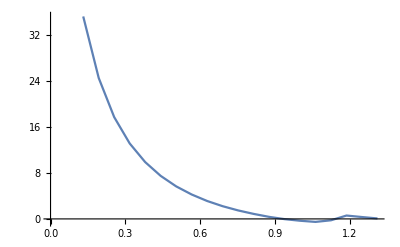

```mathematica
ListLinePlot[Thread[{Rb,A18Beta}]]
```

#### Plotting the chord length

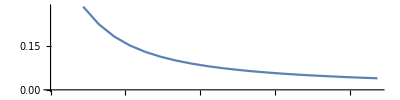

```mathematica
ListLinePlot[Thread[{Rb,A18lengthList}], AspectRatio->.25]
```

## Power Generation

### Common Calculations

#### Averaged Sections

```mathematica
For[i = 1; Rb2 = {}, i < Length[Rb], i++, AppendTo[Rb2, (Rb[[i]] + Rb[[i + 1]]) /2]]
Rb2
```

{0.162026,0.224079,0.286132,0.348184,0.410237,0.472289,0.534342,0.596395,0.658447,0.7205,0.782553,0.844605,0.906658,0.968711,1.03076,1.09282,1.15487,1.21692,1.27897}

#### Speed Ratio for Averaged Sections

```mathematica
λr2 =λd Rb2 / R1
```

{0.848368,1.17327,1.49818,1.82309,2.148,2.4729,2.79781,3.12272,3.44762,3.77253,4.09744,4.42234,4.74725,5.07216,5.39706,5.72197,6.04688,6.37178,6.69669}

### Airfoil A18

#### Average Length Sections

```mathematica
For[i = 1; A18lengthList2 = {}, i < Length[A18lengthList], i++, AppendTo[A18lengthList2, (A18lengthList[[i]] + A18lengthList[[i + 1]]) /2]]
A18lengthList2
```

{0.255845,0.204493,0.167985,0.141679,0.122131,0.10715,0.0953511,0.0858423,0.0780277,0.0714984,0.0659651,0.0612185,0.0571034,0.0535026,0.0503261,0.0475035,0.044979,0.042708,0.0406544}

#### Average Pitch Angles

```mathematica
For[i = 1; A18Beta2  = {}, i < Length[A18Beta], i++, AppendTo[A18Beta2 , (A18Beta[[i]] + A18Beta[[i + 1]]) /2]]
A18Beta2
```

{29.8919,21.1286,15.4301,11.5158,8.69339,6.58104,4.9609,3.68792,2.66841,1.84735,1.17695,0.615642,0.158966,-0.178843,-0.419437,-0.379151,0.173993,0.456037,0.202055}

#### Forces along the blade

```mathematica
A18TFList = Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18NFList = Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr];
```

```mathematica
A18TF[V_]:=Piecewise[{
{ Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18NF[V_]:=Piecewise[{
{ Total[Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2] / R1,  RPM[V,λd, R1] ≤ rpm1 },

{ Total[Fblade[A18CFN[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2] /R1,  RPM[V,λd, R1] > rpm1 } }];
```

```mathematica
A18CT[V_]:= (2 A18TF[V])/(δa π V^2 R1^2)
```

#### Out Power

```mathematica
A18Po[V_]:=Piecewise[{
{ (Z1 π)/30 RPM[V, λd, R1] Total[Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[V, V λr2], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] ≤ rpm1 },

{ (Z1 π)/30 rpm1 Total[Fblade[A18CFT[ArcTan[(60 V)/(3*Rb2 rpm1 π)]/Degree-A18Beta2, (Rb2 rpm1 π)/(30 V)], Vr[V, (Rb2 rpm1 π)/30], A18lengthList2, Δr] Rb2],  RPM[V,λd, R1] > rpm1 }
}]
```

```mathematica
A18Po[Vw]
```

4985.28

```mathematica
Pw[Vw, R1, 1]
```

11144.8

```mathematica
A18Po[Vw]/Pw[Vw, R1, 1]
```

0.447319

```mathematica
A18Po[15]/Pw[15, R1, 1]
```

0.447319

```mathematica
A18TF[Vw]
A18NF[Vw]
```

16.1513

135.706

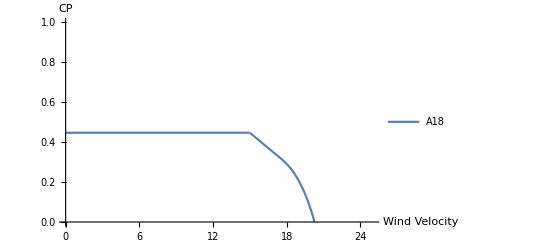

```mathematica
Plot[{A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +10}, PlotRange->{0,1},AxesLabel->{"Wind Velocity", "CP"} ,PlotLegends->{"A18"}]
```

### Chart

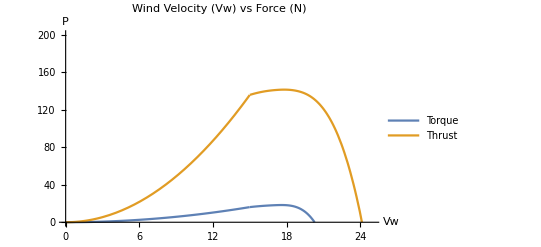

```mathematica
Plot[{A18TF[v], A18NF[v]} ,{v,0,Vw +10}, PlotRange->{0,200},PlotLabel->Style["Wind Velocity (Vw) vs Force (N)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Torque","Thrust"}]
```

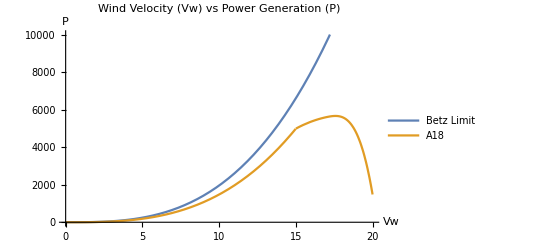

```mathematica
Plot[{Pw[v, R1, CPmax], A18Po[v]} ,{v,0,Vw +5}, PlotRange->{0,10000},PlotLabel->Style["Wind Velocity (Vw) vs Power Generation (P)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["P", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18"}]
```

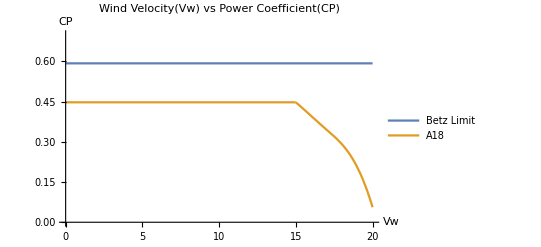

```mathematica
Plot[{Pw[v, R1, CPmax]/Pw[v, R1, 1],A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5}, PlotRange->{0,.7},PlotLabel->Style["Wind Velocity(Vw) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["Vw", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"Betz Limit","A18"}]
```

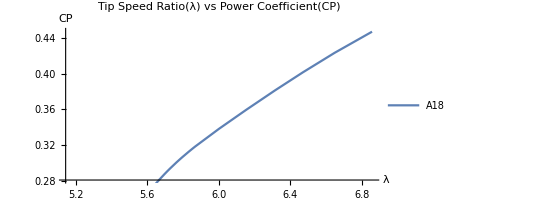

```mathematica
ParametricPlot[{TSRD[v],A18Po[v]/Pw[v, R1, 1]} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Power Coefficient(CP)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CP", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18"}, AspectRatio->1/2]
```

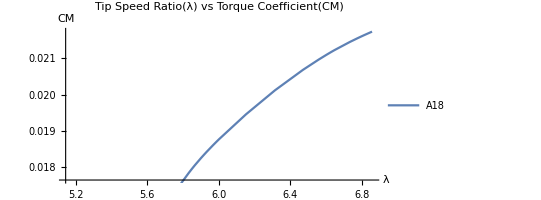

```mathematica
ParametricPlot[{TSRD[v],A18CT[v]} ,{v,0,Vw +5},PlotLabel->Style["Tip Speed Ratio(λ) vs Torque Coefficient(CM)", Black,30,FontFamily->"Times New Roman",Italic],AxesLabel->{Style["λ", Black,20,FontFamily->"Times New Roman"], Style["CM", Black,20,FontFamily->"Times New Roman",Italic]} ,PlotLegends->{"A18"}, AspectRatio->1/2]
```

## Exporting Data

### Design Data

```mathematica
SetDirectory[NotebookDirectory[]]
Export["design_data.xls",Thread[{Rb,A18lengthList,A18Beta }],"XLS"]
```

C:\Users\Jesus Rocha\Documents\GitHub\WTDesigner\A18

design_data.xls

### Generation Data

```mathematica
SetDirectory[NotebookDirectory[]]
Export["force_data.xls",Thread[{Rb2,Fblade[A18CFT[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr],Fblade[A18CFN[theta[λr2]-A18Beta2, λr2], Vr[Vw, Vw λr2], A18lengthList2, Δr] }],"XLS"]
Export["power_data.xls",Table[{v, A18Po[v]},{v,0,25,1  }],"XLS"]
```

C:\Users\Jesus Rocha\Documents\GitHub\WTDesigner\A18

force_data.xls

InterpolatingFunction::dmval: Input value {13.4274} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.1597} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.6713} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

power_data.xls

```mathematica
Pw[14.45, R1,0.51696731417262 ]
```

5150.69

```mathematica
A18Po[14.41]
```

4419.85